```mathematica
basedir="\\\\192.168.1.21\\d\\data\\Cycle 192ter\\exp_3-16-14\\rawdata\\temperedSiTest\\"
Get[basedir<>"camera_ifg.m"]
```

\\192.168.1.21\d\data\Cycle 192ter\exp_3-16-14\rawdata\temperedSiTest\

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

# heavily tempered silicon

```mathematica
filename = "rockingCam_30Sep1039.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],12;;59,11;;58]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{36,64,64} | {36,48,48}
-Graphics- | -Graphics-

```mathematica
phsh=LoadDatFile[ StringReplace["..\\temperedSiTest\\"<>filename,".tif"->".dat"]][[2]]
```

{1.3272,1.32741,1.3276,1.3278,1.32802,1.32821,1.32841,1.32861,1.32879,1.32901,1.3292,1.32941,1.32961,1.32981,1.33001,1.3302,1.33041,1.3306,1.3308,1.33099,1.3312,1.33143,1.33161,1.33182,1.33199,1.3322,1.33239,1.3326,1.3328,1.333,1.33321,1.3334,1.3336,1.33381,1.33401,1.33421}

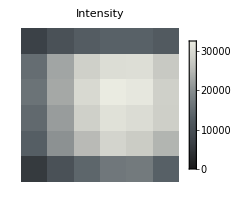
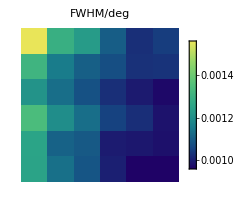
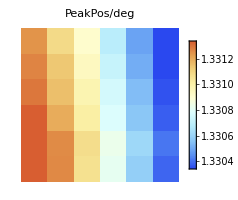

```mathematica
res=fitgridGauss[imgreduced,phsh,8,8,1,0.5];
plotresGauss[res,200,0.0003,0.0005]
```

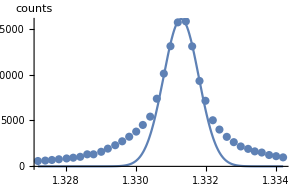
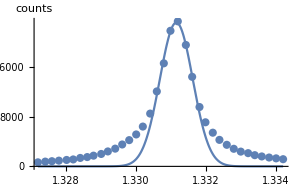
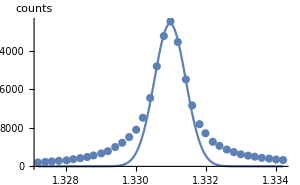
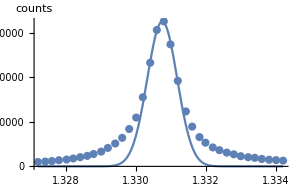
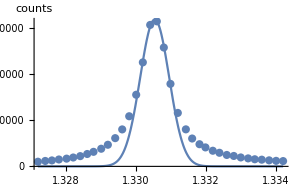
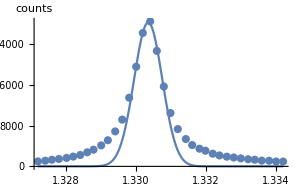
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 16061.4 | 194.059 | 82.7655 | 3.88772×10^-6
CameraIfgPackage`Private`c | 1.3313 | 7.52146×10^-6 | 177000. | 3.97699×10^-16
CameraIfgPackage`Private`d | 0.000503708 | 0.0000124292 | 40.5262 | 0.0000330608peakheight=16061.4
peakpos=1.3313
width(sigma)=0.000503708
FWHM=0.00121003
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 23086.5 | 414.412 | 55.709 | 0.0000127406
CameraIfgPackage`Private`c | 1.33116 | 0.00001032 | 128988. | 1.0276×10^-15
CameraIfgPackage`Private`d | 0.000470508 | 0.00001582 | 29.7413 | 0.0000834882peakheight=23086.5
peakpos=1.33116
width(sigma)=0.000470508
FWHM=0.00113028
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 29659.4 | 381.881 | 77.6666 | 0.000165739
CameraIfgPackage`Private`c | 1.33098 | 7.879×10^-6 | 168927. | 3.5043×10^-11
CameraIfgPackage`Private`d | 0.000448661 | 0.0000131203 | 34.1959 | 0.000854072peakheight=29659.4
peakpos=1.33098
width(sigma)=0.000448661
FWHM=0.00107779
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 32503.1 | 379.439 | 85.661 | 0.000136253
CameraIfgPackage`Private`c | 1.33076 | 6.80386×10^-6 | 195588. | 2.61405×10^-11
CameraIfgPackage`Private`d | 0.000426948 | 0.0000113123 | 37.7419 | 0.000701285peakheight=32503.1
peakpos=1.33076
width(sigma)=0.000426948
FWHM=0.00102563
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 31947.3 | 314.177 | 101.686 | 0.000096698
CameraIfgPackage`Private`c | 1.33054 | 5.57186×10^-6 | 238796. | 1.75366×10^-11
CameraIfgPackage`Private`d | 0.000414145 | 8.81279×10^-6 | 46.9936 | 0.00045251peakheight=31947.3
peakpos=1.33054
width(sigma)=0.000414145
FWHM=0.000994877
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 28242.4 | 527.804 | 53.5094 | 0.00034907
CameraIfgPackage`Private`c | 1.33035 | 9.77374×10^-6 | 136115. | 5.39744×10^-11
CameraIfgPackage`Private`d | 0.000402893 | 0.0000155474 | 25.9139 | 0.00148582peakheight=28242.4
peakpos=1.33035
width(sigma)=0.000402893
FWHM=0.000967847

```mathematica
Column[Table[showtileresGauss[res,x,2],{x,0,5}]]
```